```mathematica
GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"]
Table[Table[Table[Table[Table[
Labeled[
ArrayPlot[GraphDistanceMatrix[{{"[◼]", "BranchialGraph"}}[NestGraph[ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i4]]}]}],{Tuples[{0,1},l][[k]]},t,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"]]]/.∞->0,ColorFunction->"TemperatureMap"]
,
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->Tuples[{0,1},j][[i1]],
"b"->Tuples[{0,1},j][[i2]],
"c":>Tuples[{0,1},j][[i3]],
"d":>Tuples[{0,1},j][[i4]],
"e":>Tuples[{0,1},l][[k]]
|>]]
,{t,5,5}],
{i1,1,2},
{i2,2,2},
{i3,2,2},
{i4,2,2}],
{j,3,3}],
{k,2^(l-1),2^l}],
{l,3,3}]
```

Syntax::bktmop: Expression "GraphLayout->LayeredDigraphEmbedding,PerformanceGoal->Quality]" has no opening "[".

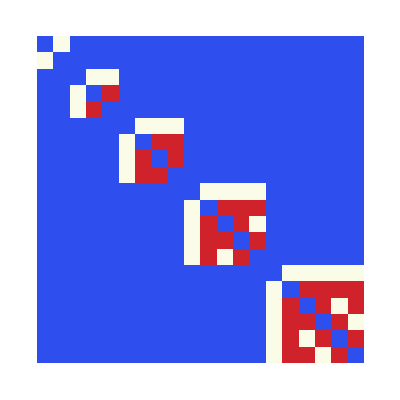
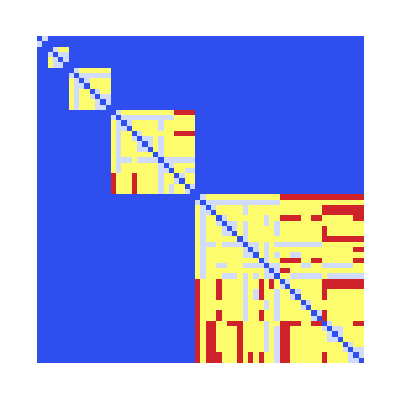
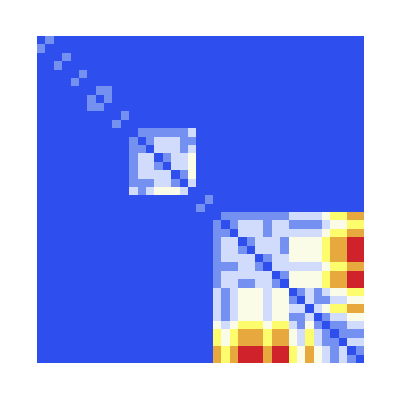
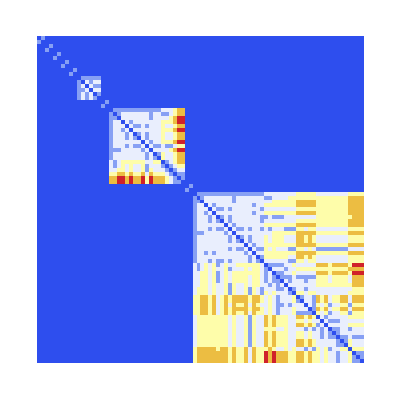
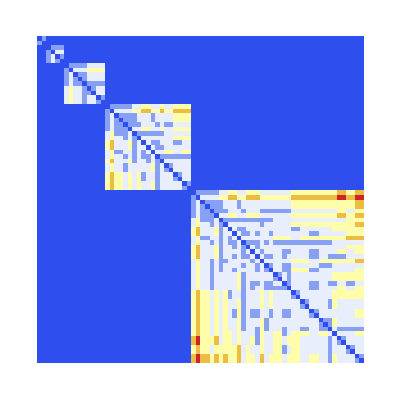
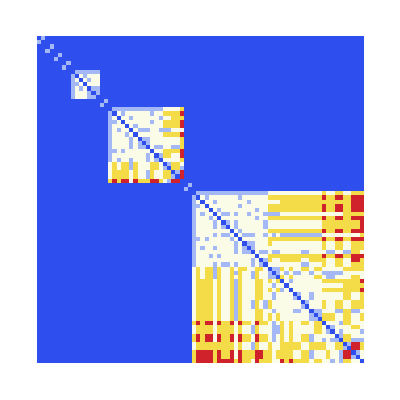
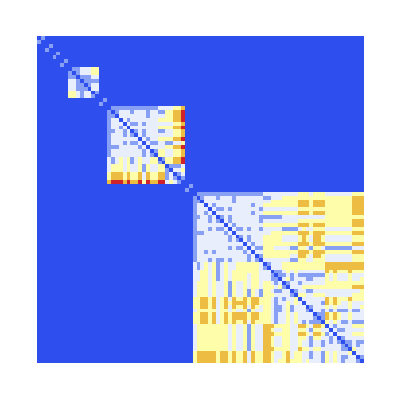
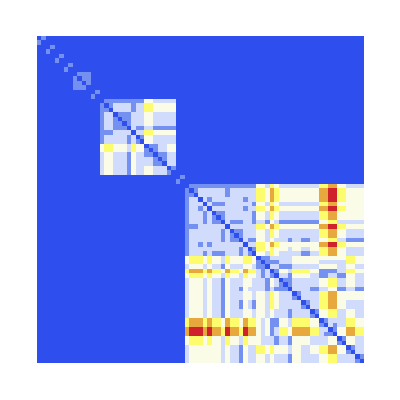
{{{{{{{{-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 0, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{0, 0, 1}}}}},{{{{-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 0, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{0, 0, 1}}}}},{{{{-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 0, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{0, 0, 1}}}}},{{{{-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 0, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{0, 0, 1}}}}},{{{{-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 0, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{0, 0, 1}}}}},{{{{-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 0, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{0, 0, 1}}}}},{{{{-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 0, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{0, 0, 1}}}}},{{{{-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 0, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{0, 0, 1}}}}}}}}}

```mathematica
Table[Table[Table[Table[Table[
Labeled[
ArrayPlot[GraphDistanceMatrix[{{"[◼]", "BranchialGraph"}}[NestGraph[ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i4]]}]}],{Tuples[{0,1},l][[k]]},t,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"]]]/.∞->0,ColorFunction->"TemperatureMap"]
,
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->Tuples[{0,1},j][[i1]],
"b"->Tuples[{0,1},j][[i2]],
"c":>Tuples[{0,1},j][[i3]],
"d":>Tuples[{0,1},j][[i4]],
"e":>Tuples[{0,1},l][[k]]
|>]]
,{t,5,5}],
{i1,1,2^j},
{i2,2,2},
{i3,2,2},
{i4,2,2}],
{j,3,3}],
{k,2,2}],
{l,3,3}]
```

```mathematica
Table[Table[Table[Table[Table[
Labeled[
NestGraph[ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i4]]}]}],{Tuples[{0,1},l][[k]]},t,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"]
,
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->Tuples[{0,1},j][[i1]],
"b"->Tuples[{0,1},j][[i2]],
"c":>Tuples[{0,1},j][[i3]],
"d":>Tuples[{0,1},j][[i4]],
"e":>Tuples[{0,1},l][[k]]
|>]]
,{t,5,5}],
{i1,1,2},
{i2,2,2},
{i3,2,2},
{i4,2,2}],
{j,3,3}],
{k,2,2}],
{l,3,3}]
```

{{{{{{{{-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 0, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{0, 0, 1}}}}},{{{{-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 0, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{0, 0, 1}}}}}}}}}